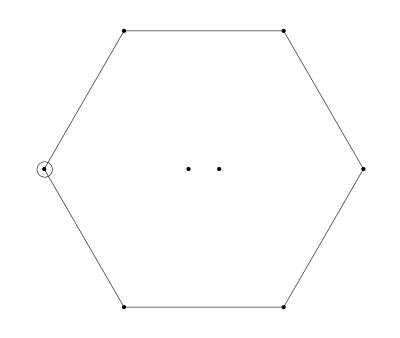

Y=0,  I_3=-1

-2dd(ūd̄+d̄ū)-(sd+ds)(ūs̄+s̄ū)-2(ud+du)ūū

```mathematica
(*-------------------------------*)
```

The current J:

(d_a^T C σ^αμ s_b) ((s̄)_b σ^αμ C((ū)_a)^T-(ū)_a σ^αμ C((s̄)_b)^T)+(s_a^T C σ^αμ d_b) ((s̄)_b σ^αμ C((ū)_a)^T-(ū)_a σ^αμ C((s̄)_b)^T)+(d_a^T C σ^αμ s_b) ((ū)_b σ^αμ C((s̄)_a)^T-(s̄)_a σ^αμ C((ū)_b)^T)+(s_a^T C σ^αμ d_b) ((ū)_b σ^αμ C((s̄)_a)^T-(s̄)_a σ^αμ C((ū)_b)^T)+2 (d_a^T C σ^αμ d_b) ((d̄)_b σ^αμ C((ū)_a)^T-(ū)_a σ^αμ C((d̄)_b)^T)+2 (d_a^T C σ^αμ d_b) ((ū)_b σ^αμ C((d̄)_a)^T-(d̄)_a σ^αμ C((ū)_b)^T)+2 ((ū)_b σ^αμ C((ū)_a)^T-(ū)_a σ^αμ C((ū)_b)^T) (d_a^T C σ^αμ u_b)+2 ((ū)_b σ^αμ C((ū)_a)^T-(ū)_a σ^αμ C((ū)_b)^T) (u_a^T C σ^αμ d_b)

the Fierz rearranged J (to naively get the decay partten)

```mathematica
-12 (2 (d̄(γ̄)^5 d)+s̄(γ̄)^5 s) (ū(γ̄)^5 d)-12 (s̄(γ̄)^5 d ū(γ̄)^5 s)-2 (s̄ σ^μν d ū σ^μν s)-2 (s̄ σ^μν s ū σ^μν d)-12 (2 (d̄ 1d)+s̄ 1s) (ū 1d)-12 (s̄ 1d ū 1s)-24 (ū(γ̄)^5 d ū(γ̄)^5 u)-4 (d̄ σ^μν d ū σ^μν d)-4 (ū σ^μν d ū σ^μν u)-24 (ū 1d ū 1u)
```

Π(q^2)=
-(log(-q^2/μ^2) q^8)/(32 π^6)-(5 ⟨ GG ⟩ log(-q^2/μ^2) q^4)/(12 π^5)-(9 ⟨ d̄ d⟩ log(-q^2/μ^2) m_d q^4)/π^4-(2 ⟨ s̄ s⟩ log(-q^2/μ^2) m_s q^4)/π^4-(9 ⟨ ū u⟩ log(-q^2/μ^2) m_u q^4)/π^4-(96 ⟨ d̄ d⟩^2 log(-q^2/μ^2) q^2)/π^2-(24 ⟨ s̄ s⟩^2 log(-q^2/μ^2) q^2)/π^2-(96 ⟨ ū u⟩^2 log(-q^2/μ^2) q^2)/π^2+(5 ⟨G^3⟩ log(-q^2/μ^2) q^2)/(4 π^6)-(96 ⟨ d̄ d⟩ ⟨ s̄ s⟩ log(-q^2/μ^2) q^2)/π^2-(192 ⟨ d̄ d⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/π^2-(96 ⟨ s̄ s⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/π^2+(32 ⟨ d̄ d⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/π^2+(16 ⟨ s̄ s⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/π^2+(32 ⟨ ū u⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/π^2+(16 ⟨ d̄ d⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/π^2+(8 ⟨ s̄ s⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/π^2+(16 ⟨ ū u⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/π^2+(32 ⟨ d̄ d⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/π^2+(16 ⟨ s̄ s⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/π^2+(32 ⟨ ū u⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/π^2-(32 ⟨ GG ⟩ ⟨ d̄ d⟩^2)/(π q^2)-(8 ⟨ GG ⟩ ⟨ s̄ s⟩^2)/(π q^2)-(32 ⟨ GG ⟩ ⟨ ū u⟩^2)/(π q^2)-(2 ⟨ d̄ Gd⟩^2)/(3 π^2 q^2)-⟨ s̄ Gs⟩^2/(6 π^2 q^2)-(2 ⟨ ū Gu⟩^2)/(3 π^2 q^2)-(32 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ s̄ s⟩)/(π q^2)-(64 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ ū u⟩)/(π q^2)-(32 ⟨ GG ⟩ ⟨ s̄ s⟩ ⟨ ū u⟩)/(π q^2)-(2 ⟨ d̄ Gd⟩ ⟨ s̄ Gs⟩)/(3 π^2 q^2)-(4 ⟨ d̄ Gd⟩ ⟨ ū Gu⟩)/(3 π^2 q^2)-(2 ⟨ s̄ Gs⟩ ⟨ ū Gu⟩)/(3 π^2 q^2)-(128 ⟨ s̄ s⟩ ⟨ ū u⟩^2 (2 m_d+m_u))/q^2-(128 ⟨ d̄ d⟩^2 ⟨ s̄ s⟩ (m_d+2 m_u))/q^2-(16 ⟨ d̄ d⟩ ⟨ s̄ s⟩^2 (6 m_d+4 m_u))/(3 q^2)-(64 ⟨ d̄ d⟩ ⟨ ū u⟩^2 (10 m_d+4 m_u))/q^2-(16 ⟨ s̄ s⟩^2 ⟨ ū u⟩ (4 m_d+6 m_u))/(3 q^2)-(64 ⟨ ū u⟩^3 (8 m_d+6 m_u))/(3 q^2)-(64 ⟨ d̄ d⟩^3 (6 m_d+8 m_u))/(3 q^2)-(64 ⟨ d̄ d⟩^2 ⟨ ū u⟩ (4 m_d+10 m_u))/q^2-(64 ⟨ d̄ d⟩ ⟨ s̄ s⟩ ⟨ ū u⟩ (18 m_d-4 m_s+18 m_u))/(3 q^2)

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for η_6=η_8=η_10=1

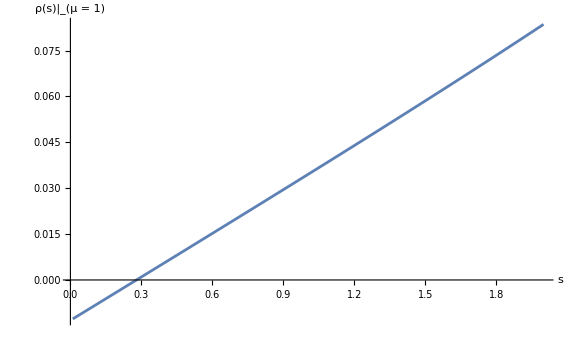
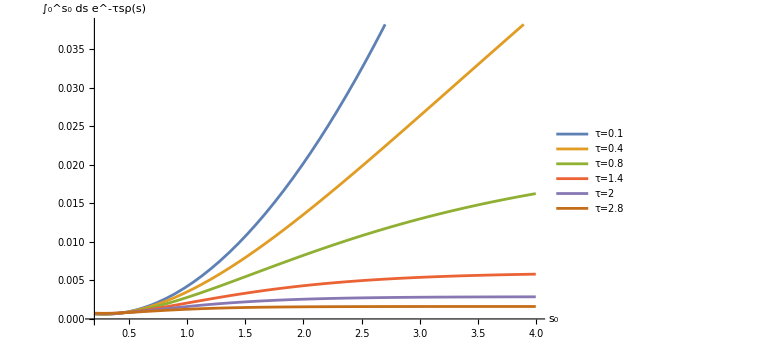

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for η_6=η_8=η_10=1

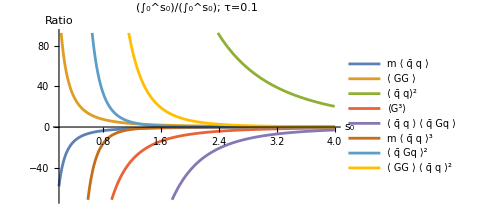
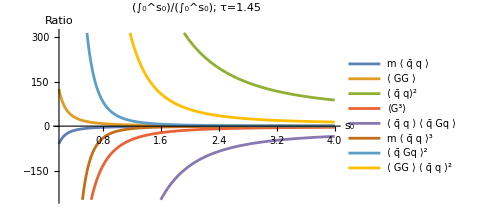
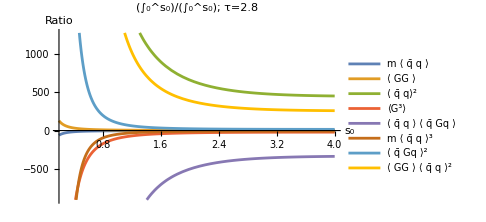

```mathematica
(*-------------------------------*)
```

ℛ^0 for η_6=η_8=η_10=1

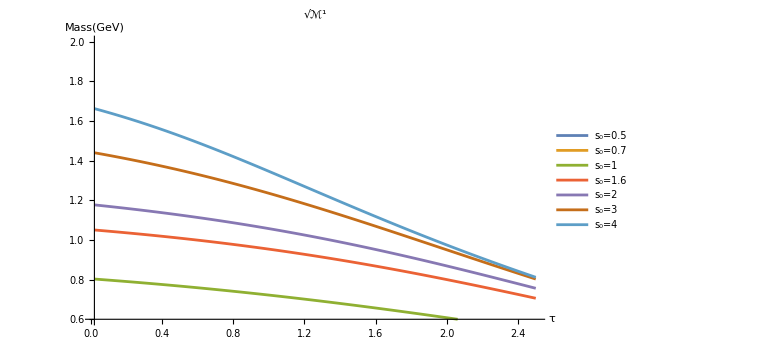
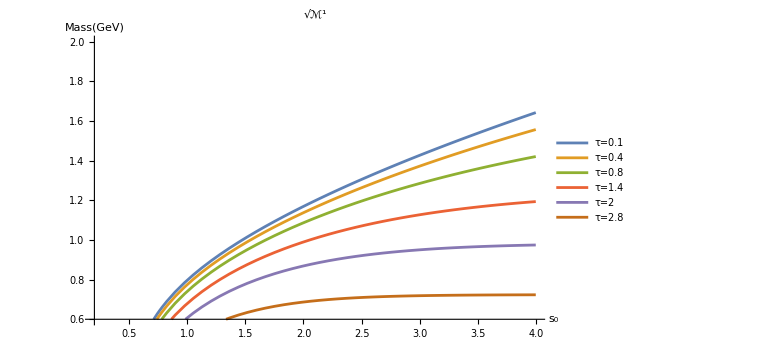

```mathematica
(*-------------------------------*)
```

ℛ^1 for η_6=η_8=η_10=1

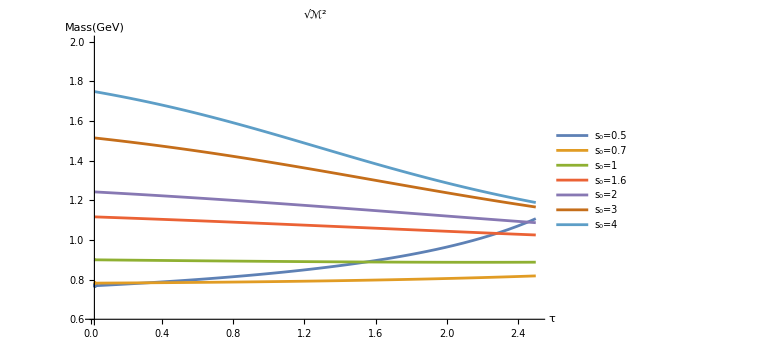
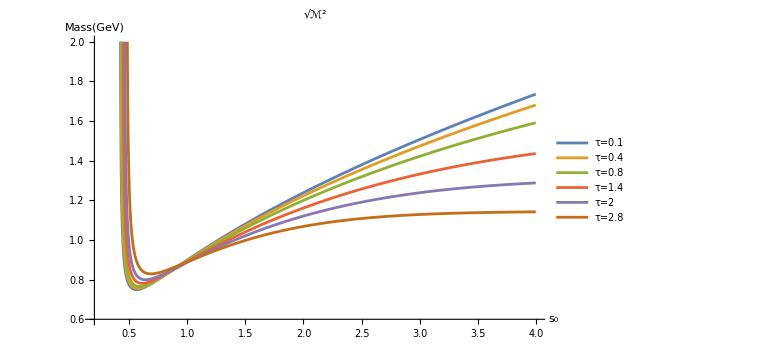

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for η_6=3, η_8=5, η_10=5

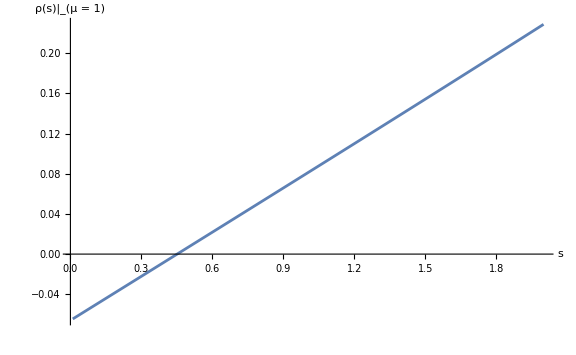
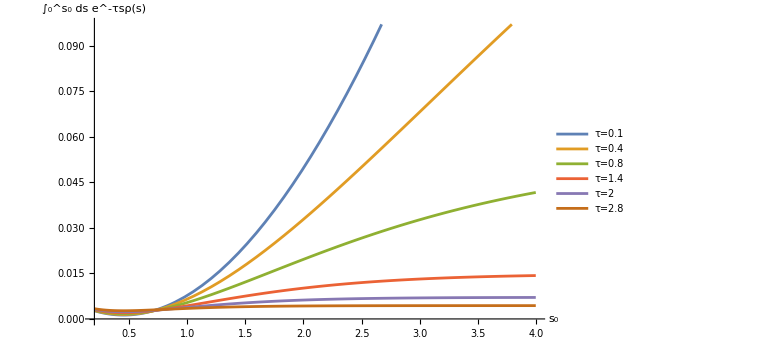

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for η_6=3, η_8=5, η_10=5

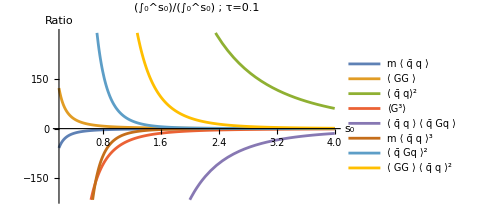
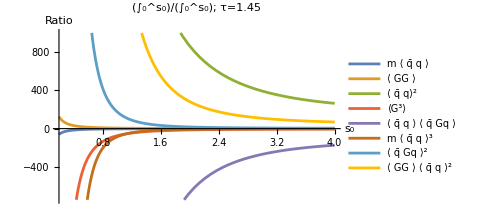
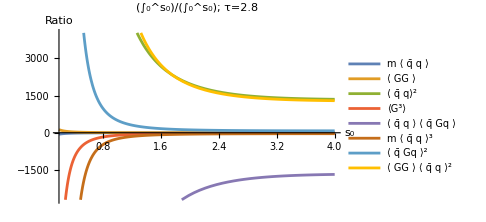

```mathematica
(*-------------------------------*)
```

ℛ^0 for η_6=3, η_8=5, η_10=5

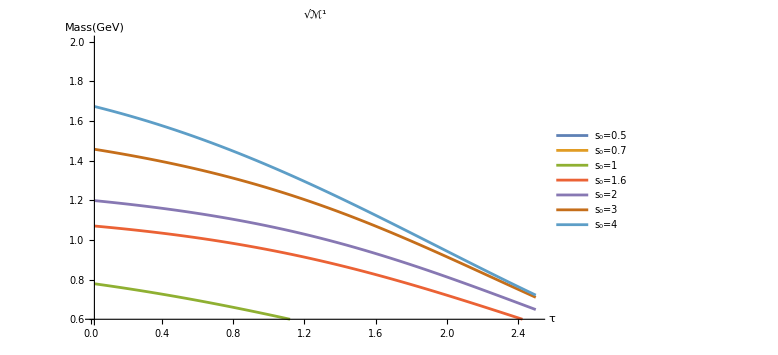
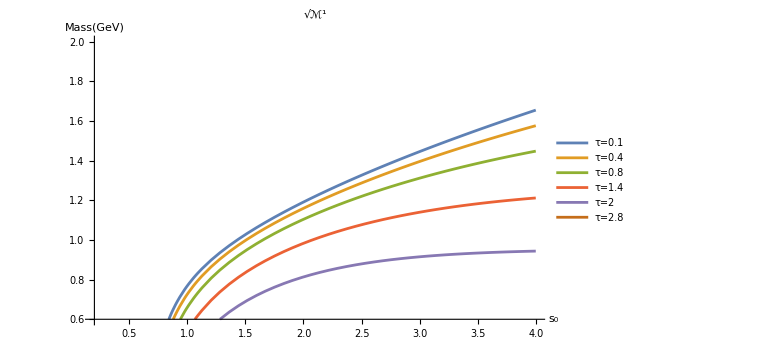

```mathematica
(*-------------------------------*)
```

ℛ^1 for η_6=3, η_8=5, η_10=5